Lucas Asset Pricing Under CRRA Utility

IID Dividends

```mathematica
ClearAll["Global`*"];
LogNormalDistribution[-σ^2/2,σ];
𝔼d = Expectation[dtpn,dtpn \[Distributed] LogNormalDistribution[-σ^2/2,σ]];
𝔼dTo1mρ = Expectation[dtpn^(1-ρ),dtpn \[Distributed] LogNormalDistribution[-σ^2/2,σ]];
```

ⅇ^(1/2 (-1+ρ) ρ σ^2)

1

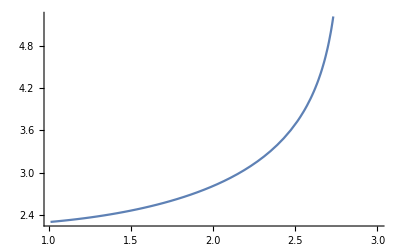

```mathematica
θ=0.1;σ=0.2;
Plot[-Log[θ-(1/2)ρ(ρ-1)σ^2],{ρ,1.01,3}]
```

```mathematica
ρ
```

ρ